```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,5}]//tf
Select[nCollatz[33],OddQ]
nFaulhaber[2,4]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125

{33,25,19,29,11,17,13,5,1}

30

## Queue MMa.SE Questions

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

### Q.1

```mathematica
DirichletConvolve[1,u[n],n,m]//FullForm
```

DivisorSum[m,Function[u[Slot[1]]]]

### Q.2

```mathematica
DirichletTransform[Abs[MoebiusMu[n]],n,s]
```

Zeta[s]/Zeta[2 s]

```mathematica
DirichletTransform[MoebiusMu[n]^2,n,s]
```

DirichletTransform[MoebiusMu[n]^2,n,s]

```mathematica
Table[{k,Abs[MoebiusMu[k]],MoebiusMu[k]^2},{k,1,6}]//tf
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 1 | 1

## Topic

### Definition / Theorem

This is text.

#### Example

# Algebraic Number Theory

Introduction

A crash course in Ring Theory

## Basic Definitions

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Ideals, Homomorphisms, and Quotients

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Principal Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Operations on Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Prime and Maximal Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

Lattices

## Group Structure of Lattices

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Linear Algebra over ℤ

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Computing with Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Lattice Quotients

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

Arithmetic in Q[d]

## Quadratic Fields

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## The Ring of Integers

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Unique Factorization of Ideals: The Roadmap

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Noether Rings

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Standard Form of an Ideal

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## The Ideal Norm

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Fractional Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Unique Factorization of Ideals

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

## Prime Ideals in O

### Definition / Theorem

[ TBD ]

#### Proof

[ TBD ]

□

#### Example

The Ideal Class Group and the Geometry of Numbers

Continued Fractions

Quadratic Forms

Notes

```mathematica
Needs["AbstractAlgebra`Master`"]
```

```mathematica
SwitchStructureTo[Ring];
```

```mathematica
R1=Z[3,I,Structure->Ring]
CayleyTables[R1,Mode->Visual]
```

Ringoid[{0,ⅈ,2 ⅈ,1,1+ⅈ,1+2 ⅈ,2,2+ⅈ,2+2 ⅈ},-Addition-,-Multiplication-]

+ | 0 | ⅈ | 2 ⅈ | 1 | 1+ⅈ | 1+2 ⅈ | 2 | 2+ⅈ | 2+2 ⅈ
0 | 0 | ⅈ | 2 ⅈ | 1 | 1+ⅈ | 1+2 ⅈ | 2 | 2+ⅈ | 2+2 ⅈ
ⅈ | ⅈ | 2 ⅈ | 0 | 1+ⅈ | 1+2 ⅈ | 1 | 2+ⅈ | 2+2 ⅈ | 2
2 ⅈ | 2 ⅈ | 0 | ⅈ | 1+2 ⅈ | 1 | 1+ⅈ | 2+2 ⅈ | 2 | 2+ⅈ
1 | 1 | 1+ⅈ | 1+2 ⅈ | 2 | 2+ⅈ | 2+2 ⅈ | 0 | ⅈ | 2 ⅈ
1+ⅈ | 1+ⅈ | 1+2 ⅈ | 1 | 2+ⅈ | 2+2 ⅈ | 2 | ⅈ | 2 ⅈ | 0
1+2 ⅈ | 1+2 ⅈ | 1 | 1+ⅈ | 2+2 ⅈ | 2 | 2+ⅈ | 2 ⅈ | 0 | ⅈ
2 | 2 | 2+ⅈ | 2+2 ⅈ | 0 | ⅈ | 2 ⅈ | 1 | 1+ⅈ | 1+2 ⅈ
2+ⅈ | 2+ⅈ | 2+2 ⅈ | 2 | ⅈ | 2 ⅈ | 0 | 1+ⅈ | 1+2 ⅈ | 1
2+2 ⅈ | 2+2 ⅈ | 2 | 2+ⅈ | 2 ⅈ | 0 | ⅈ | 1+2 ⅈ | 1 | 1+ⅈ  Add.* | 0 | ⅈ | 2 ⅈ | 1 | 1+ⅈ | 1+2 ⅈ | 2 | 2+ⅈ | 2+2 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 2 | 1 | ⅈ | 2+ⅈ | 1+ⅈ | 2 ⅈ | 2+2 ⅈ | 1+2 ⅈ
2 ⅈ | 0 | 1 | 2 | 2 ⅈ | 1+2 ⅈ | 2+2 ⅈ | ⅈ | 1+ⅈ | 2+ⅈ
1 | 0 | ⅈ | 2 ⅈ | 1 | 1+ⅈ | 1+2 ⅈ | 2 | 2+ⅈ | 2+2 ⅈ
1+ⅈ | 0 | 2+ⅈ | 1+2 ⅈ | 1+ⅈ | 2 ⅈ | 2 | 2+2 ⅈ | 1 | ⅈ
1+2 ⅈ | 0 | 1+ⅈ | 2+2 ⅈ | 1+2 ⅈ | 2 | ⅈ | 2+ⅈ | 2 ⅈ | 1
2 | 0 | 2 ⅈ | ⅈ | 2 | 2+2 ⅈ | 2+ⅈ | 1 | 1+2 ⅈ | 1+ⅈ
2+ⅈ | 0 | 2+2 ⅈ | 1+ⅈ | 2+ⅈ | 1 | 2 ⅈ | 1+2 ⅈ | ⅈ | 2
2+2 ⅈ | 0 | 1+2 ⅈ | 2+ⅈ | 2+2 ⅈ | ⅈ | 1 | 1+ⅈ | 2 | 2 ⅈ  Mult.

```mathematica
R2=Z[20,5]
CayleyTables[R2,Mode->Visual]
```

Ringoid[{0,5,10,15},Mod[#1+#2,20]&,Mod[#1 #2,20]&]

+ | 0 | 5 | 10 | 15
0 | 0 | 5 | 10 | 15
5 | 5 | 10 | 15 | 0
10 | 10 | 15 | 0 | 5
15 | 15 | 0 | 5 | 10  Add.* | 0 | 5 | 10 | 15
0 | 0 | 0 | 0 | 0
5 | 0 | 5 | 10 | 15
10 | 0 | 10 | 0 | 10
15 | 0 | 15 | 10 | 5  Mult.

```mathematica
RingQ[R2]
FieldQ[R2]
Units[R2]
```

True

False

{5,15}

```mathematica
FieldQ[Z[30,6]]
```

True

```mathematica
M=Mat[Z[2],{2,2}]
```

-Mat_2(Z[2])-

```mathematica
Map[#//mf&,Domain[M]]
```

{(0 | 0
0 | 0),(0 | 0
0 | 1),(0 | 0
1 | 0),(0 | 0
1 | 1),(0 | 1
0 | 0),(0 | 1
0 | 1),(0 | 1
1 | 0),(0 | 1
1 | 1),(1 | 0
0 | 0),(1 | 0
0 | 1),(1 | 0
1 | 0),(1 | 0
1 | 1),(1 | 1
0 | 0),(1 | 1
0 | 1),(1 | 1
1 | 0),(1 | 1
1 | 1)}

```mathematica
R3=ToRingoid[Mat[Z[2],2]]
```

Ringoid[{{{0,0},{0,0}},{{0,0},{0,1}},{{0,0},{1,0}},{{0,0},{1,1}},{{0,1},{0,0}},{{0,1},{0,1}},{{0,1},{1,0}},{{0,1},{1,1}},{{1,0},{0,0}},{{1,0},{0,1}},{{1,0},{1,0}},{{1,0},{1,1}},{{1,1},{0,0}},{{1,1},{0,1}},{{1,1},{1,0}},{{1,1},{1,1}}},-Addition-,-Multiplication-]

```mathematica
RingQ[R3]
```

True

```mathematica
CayleyTables[R3,Mode->Visual]
```

+ | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g1 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g2 | g2 | g1 | g4 | g3 | g6 | g5 | g8 | g7 | g10 | g9 | g12 | g11 | g14 | g13 | g16 | g15
g3 | g3 | g4 | g1 | g2 | g7 | g8 | g5 | g6 | g11 | g12 | g9 | g10 | g15 | g16 | g13 | g14
g4 | g4 | g3 | g2 | g1 | g8 | g7 | g6 | g5 | g12 | g11 | g10 | g9 | g16 | g15 | g14 | g13
g5 | g5 | g6 | g7 | g8 | g1 | g2 | g3 | g4 | g13 | g14 | g15 | g16 | g9 | g10 | g11 | g12
g6 | g6 | g5 | g8 | g7 | g2 | g1 | g4 | g3 | g14 | g13 | g16 | g15 | g10 | g9 | g12 | g11
g7 | g7 | g8 | g5 | g6 | g3 | g4 | g1 | g2 | g15 | g16 | g13 | g14 | g11 | g12 | g9 | g10
g8 | g8 | g7 | g6 | g5 | g4 | g3 | g2 | g1 | g16 | g15 | g14 | g13 | g12 | g11 | g10 | g9
g9 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8
g10 | g10 | g9 | g12 | g11 | g14 | g13 | g16 | g15 | g2 | g1 | g4 | g3 | g6 | g5 | g8 | g7
g11 | g11 | g12 | g9 | g10 | g15 | g16 | g13 | g14 | g3 | g4 | g1 | g2 | g7 | g8 | g5 | g6
g12 | g12 | g11 | g10 | g9 | g16 | g15 | g14 | g13 | g4 | g3 | g2 | g1 | g8 | g7 | g6 | g5
g13 | g13 | g14 | g15 | g16 | g9 | g10 | g11 | g12 | g5 | g6 | g7 | g8 | g1 | g2 | g3 | g4
g14 | g14 | g13 | g16 | g15 | g10 | g9 | g12 | g11 | g6 | g5 | g8 | g7 | g2 | g1 | g4 | g3
g15 | g15 | g16 | g13 | g14 | g11 | g12 | g9 | g10 | g7 | g8 | g5 | g6 | g3 | g4 | g1 | g2
g16 | g16 | g15 | g14 | g13 | g12 | g11 | g10 | g9 | g8 | g7 | g6 | g5 | g4 | g3 | g2 | g1  Add.KEY for Add(-Mat   (Z[2])-)
        (2): label used → element: …* | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1 | g1
g2 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4 | g1 | g2 | g3 | g4
g3 | g1 | g1 | g1 | g1 | g2 | g2 | g2 | g2 | g3 | g3 | g3 | g3 | g4 | g4 | g4 | g4
g4 | g1 | g2 | g3 | g4 | g2 | g1 | g4 | g3 | g3 | g4 | g1 | g2 | g4 | g3 | g2 | g1
g5 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13 | g1 | g5 | g9 | g13
g6 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16 | g1 | g6 | g11 | g16
g7 | g1 | g5 | g9 | g13 | g2 | g6 | g10 | g14 | g3 | g7 | g11 | g15 | g4 | g8 | g12 | g16
g8 | g1 | g6 | g11 | g16 | g2 | g5 | g12 | g15 | g3 | g8 | g9 | g14 | g4 | g7 | g10 | g13
g9 | g1 | g1 | g1 | g1 | g5 | g5 | g5 | g5 | g9 | g9 | g9 | g9 | g13 | g13 | g13 | g13
g10 | g1 | g2 | g3 | g4 | g5 | g6 | g7 | g8 | g9 | g10 | g11 | g12 | g13 | g14 | g15 | g16
g11 | g1 | g1 | g1 | g1 | g6 | g6 | g6 | g6 | g11 | g11 | g11 | g11 | g16 | g16 | g16 | g16
g12 | g1 | g2 | g3 | g4 | g6 | g5 | g8 | g7 | g11 | g12 | g9 | g10 | g16 | g15 | g14 | g13
g13 | g1 | g5 | g9 | g13 | g5 | g1 | g13 | g9 | g9 | g13 | g1 | g5 | g13 | g9 | g5 | g1
g14 | g1 | g6 | g11 | g16 | g5 | g2 | g15 | g12 | g9 | g14 | g3 | g8 | g13 | g10 | g7 | g4
g15 | g1 | g5 | g9 | g13 | g6 | g2 | g14 | g10 | g11 | g15 | g3 | g7 | g16 | g12 | g8 | g4
g16 | g1 | g6 | g11 | g16 | g6 | g1 | g16 | g11 | g11 | g16 | g1 | g6 | g16 | g11 | g6 | g1  Mult.

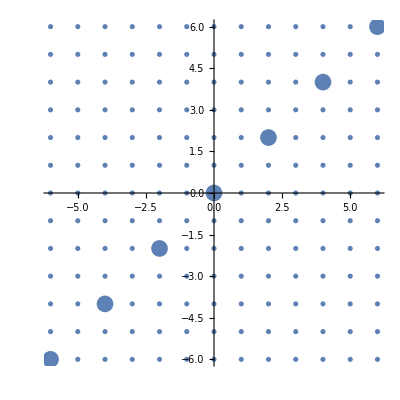

```mathematica
gr=IntegerLatticeGrid[{-6,6},{-6,6},AspectRatio->Automatic];
z=2+2I;
someMultipliers=Table[k,{k,-3,3}];
idealList = someMultipliers * z;
plotOfIdeals=ListPlot[Map[ComplexToPoint,idealList],PlotStyle->{PointSize[0.030],RGBColor[l,0,O]},DisplayFunction->Identity];
Show[{gr,plotOfIdeals}]
```

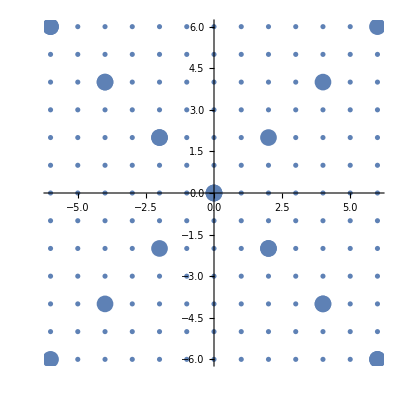

```mathematica
addToIdealList=Table[k I,{k,-3,3}] z;
idealList=Join[idealList,addToIdealList];
plotOfIdeals=ListPlot[Map[ComplexToPoint,idealList],PlotStyle->{PointSize[0.030],RGBColor[l,0,O]},AspectRatio->Automatic,DisplayFunction->Identity];
Show[{gr,plotOfIdeals}]
```

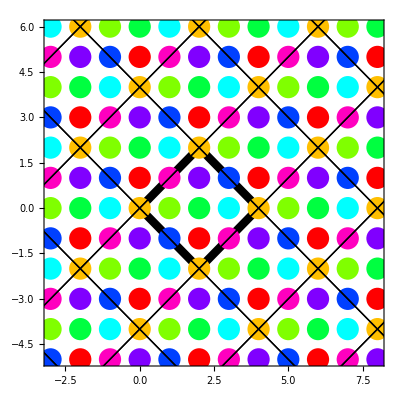

```mathematica
QuotientRing[Z[I],2+2I,Mode->Visual,Form->Representatives]
```

```mathematica
QuotientRing[Z[I],2+2I]
```

Ringoid[{J,1+J,2+J,3+J,(3+ⅈ)+J,(2+ⅈ)+J,(1+ⅈ)+J,(2-ⅈ)+J},-Addition-,-Multiplication-]

```mathematica
R=Z[45];
B1={0,15,30};
B2={0,9,18,27,36};
IdealQ[B1,R]
IdealQ[B2,R]
CayleyTables[QuotientRing[R,B2],Mode->Visual]
```

True

True

+ | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
1+NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS
2+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS
3+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS
4+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS
5+NS | 5+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS
6+NS | 6+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS
7+NS | 7+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS
8+NS | 8+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS  Add.* | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
NS | NS | NS | NS | NS | NS | NS | NS | NS | NS
1+NS | NS | 1+NS | 2+NS | 3+NS | 4+NS | 5+NS | 6+NS | 7+NS | 8+NS
2+NS | NS | 2+NS | 4+NS | 6+NS | 8+NS | 1+NS | 3+NS | 5+NS | 7+NS
3+NS | NS | 3+NS | 6+NS | NS | 3+NS | 6+NS | NS | 3+NS | 6+NS
4+NS | NS | 4+NS | 8+NS | 3+NS | 7+NS | 2+NS | 6+NS | 1+NS | 5+NS
5+NS | NS | 5+NS | 1+NS | 6+NS | 2+NS | 7+NS | 3+NS | 8+NS | 4+NS
6+NS | NS | 6+NS | 3+NS | NS | 6+NS | 3+NS | NS | 6+NS | 3+NS
7+NS | NS | 7+NS | 5+NS | 3+NS | 1+NS | 8+NS | 6+NS | 4+NS | 2+NS
8+NS | NS | 8+NS | 7+NS | 6+NS | 5+NS | 4+NS | 3+NS | 2+NS | 1+NS  Mult.